```mathematica
(*Tensor of triangle*)
Tensor=Table[0,{i,1,3},{j,1,3},{k,1,3}];
Tensor[[2,2,2]]=1;
Tensor[[1,1,2]]=-1;
Tensor[[1,2,1]]=-1;
Tensor[[2,1,1]]=-1;
```

```mathematica
Tensor//MatrixForm
```

((0
-1
0) | (-1
0
0) | (0
0
0)
(-1
0
0) | (0
1
0) | (0
0
0)
(0
0
0) | (0
0
0) | (0
0
0))

```mathematica
(*Get the rotation matrix along z, for positive rotflake, flake rotates anticlockwise*)
(*Get the rotation matrix along -y, for positive tiltflake, flake rotates in xz plane anticlockwise*)
R1[rotflake_]:=Transpose[{{Cos[rotflake],Sin[rotflake],0},{-Sin[rotflake],Cos[rotflake],0},{0,0,1}}]
R2[tiltflake_]:=Transpose[{{Cos[tiltflake],0,Sin[tiltflake]},{0,1,0},{-Sin[tiltflake],0,Cos[tiltflake]}}]
R[rotflake_,tiltflake_]:=R2[tiltflake].R1[rotflake]
```

```mathematica
(*Get the SHG tensor after flake rotation and tilt*)
RotTensor[rotflake_,tiltflake_]:=Table[(R[rotflake,tiltflake][[i,;;]].Tensor[[;;,;;,;;]].Inverse[R[rotflake,tiltflake]][[;;,j]]).Inverse[R[rotflake,tiltflake]][[;;,k]],{i,1,3},{j,1,3},{k,1,3}]
```

```mathematica
(*Get the SHG tensor for nanoscroll, roll direction is determined by rotflake*)
NanoscrollTensor[rotflake_,elp_]:=Sum[RotTensor[rotflake,ArcTan[(1+elp)^2 Cos[tiltflake],(1-elp)^2  Sin[tiltflake]]]*1/2 √(((-1+elp^2)^2 (1+6 elp^2+elp^4+4 (elp+elp^3) Cos[2 tiltflake]))/((1+elp^2+2 elp Cos[2 tiltflake])^3))*0.05,{tiltflake,0,2Pi,0.05}]/Sum[1/2 √(((-1+elp^2)^2 (1+6 elp^2+elp^4+4 (elp+elp^3) Cos[2 tiltflake]))/((1+elp^2+2 elp Cos[2 tiltflake])^3))*0.05,{tiltflake,0,2Pi,0.05}]
(*Rotate the Nanoscroll， positive for anticlockwise*)
R3[rotnanoscroll_]:=Transpose[{{Cos[rotnanoscroll],Sin[rotnanoscroll],0},{-Sin[rotnanoscroll],Cos[rotnanoscroll],0},{0,0,1}}]
(*roll and rotate roll*)
RotNanoscrollTensor[rotflake_,rotnanoscroll_,elp_]:=Table[(R3[rotnanoscroll][[i,;;]].NanoscrollTensor[rotflake,elp][[;;,;;,;;]].Inverse[R3[rotnanoscroll]][[;;,j]]).Inverse[R3[rotnanoscroll]][[;;,k]],{i,1,3},{j,1,3},{k,1,3}]
```

```mathematica
Len[rotflake_,elp_]:=Sum[1/2 √(((-1+elp^2)^2 (1+6 elp^2+elp^4+4 (elp+elp^3) Cos[2 tiltflake]))/((1+elp^2+2 elp Cos[2 tiltflake])^3))*0.001,{tiltflake,0,2Pi,0.01}]
```

```mathematica
RotNanoscrollTensor[0,0,-0.99]//MatrixForm
```

((0.
-0.0160851
0.) | (-0.0160851
0.
-0.00211255) | (0.
-0.00211255
0.)
(-0.0160851
0.
-0.00211255) | (0.
1.
0.) | (-0.00211255
0.
-0.983915)
(0.
-0.00211255
0.) | (-0.00211255
0.
-0.983915) | (0.
-0.983915
0.))

```mathematica
roll0=0/180*Pi;
rot0=0/180*Pi;
elp0=-0.6;
A0=1;
Erot[theta_]:={Cos[theta],Sin[theta],0};
f[rot_,roll_,elp_]:=Module[{tensor=RotNanoscrollTensor[-roll,roll+rot,elp]},Table[{x,A0*((tensor.Erot[x].Erot[x])[[1]])^2},{x,0,2Pi,0.05}]]
g[rot_,roll_,elp_]:=Module[{tensor=RotNanoscrollTensor[-roll,roll+rot,elp]},Table[{x,A0*((tensor.Erot[x].Erot[x])[[2]])^2},{x,0,2Pi,0.05}]]
h[rot_,roll_,elp_]:=Module[{tensor=RotNanoscrollTensor[-roll,roll+rot,elp]},Table[{x,A0*((tensor.Erot[x].Erot[x])[[1]]*Cos[x]+(tensor.Erot[x].Erot[x])[[2]]*Sin[x])^2},{x,0,2Pi,0.01}]]
i[rot_,roll_,elp_]:=Module[{tensor=RotNanoscrollTensor[-roll,roll+rot,elp]},Table[{x,A0*((tensor.Erot[x].Erot[x])[[1]]*Sin[x]-(tensor.Erot[x].Erot[x])[[2]]*Cos[x])^2},{x,0,2Pi,0.01}]]
```

```mathematica
ans1=h[rot0,roll0,elp0];
ans2=i[rot0,roll0,elp0];
```

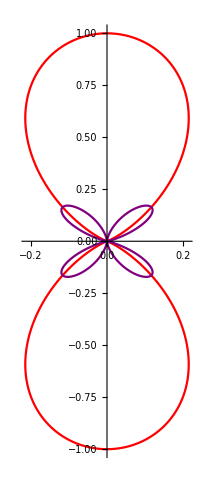

```mathematica
ListPolarPlot[{ans1,ans2},Joined->True,PlotStyle->{Red,Purple},PlotRange->All]
```

```mathematica
Export[NotebookDirectory[]<>"output1.xlsx",ans1]
Export[NotebookDirectory[]<>"output2.xlsx",ans2]
```

D:\Users\qqk\Desktop\output1.xlsx

D:\Users\qqk\Desktop\output2.xlsx

```mathematica
Erot={E0*Cos[theta],E0*Sin[theta],0};
RotTensor[x,0].Erot.Erot//FullSimplify//MatrixForm
```

(-E0^2 Sin[2 theta-3 x]
-E0^2 Cos[2 theta-3 x]
0)

```mathematica
(-E0^2 Sin[2 theta-3 *phi])^2
```

E0^4 Sin[3 phi-2 theta]^2

```mathematica
(-E0^2 Sin[2 theta-3 *phi]*Cos[theta]-E0^2 Cos[2 theta-3 phi]*Sin[theta])^2//FullSimplify
```

E0^4 Sin[3 (phi-theta)]^2

```mathematica
(E0^2 Sin[2 theta-3 *phi]*Sin[theta]-E0^2 Cos[2 theta-3 phi]*Cos[theta])^2//FullSimplify
```

E0^4 Cos[3 (phi-theta)]^2

```mathematica
a=(1+elp)/2;
b=(1-elp)/2;
```

```mathematica
(a^2-b^2)/a^2//Simplify
```

```mathematica
(1-elp)^2/(1+elp)^2
```

1-(4 elp)/(1+elp)^2

```mathematica
(*a+b=1;
(a-b)/(a+b)=elp;
a=(1+elp)/2;
b=(1-elp)/2;*)
x0=-Sin[t]*√(1/(Sin[t]^2/((1+elp)/2)^2+Cos[t]^2/((1-elp)/2)^2));
y0=Cos[t]*√(1/(Sin[t]^2/((1+elp)/2)^2+Cos[t]^2/((1-elp)/2)^2));
√(D[x0,t]^2+D[y0,t]^2)//FullSimplify
```

1/2 √(((-1+elp^2)^2 (1+6 elp^2+elp^4+4 (elp+elp^3) Cos[2 t]))/((1+elp^2+2 elp Cos[2 t])^3))

```mathematica
D[x0,t]//FullSimplify
```

```mathematica
D[y0,t]//FullSimplify
```

-2 √2 (-(-1+elp2)/(2-elp2+elp2 Cos[2 t]))^(3/2) Sin[t]

```mathematica
ans=Table[{elp,NanoscrollTensor[0,elp][[1,1,2]]},{elp,-0.99,0.99,0.1}]
```

{{-0.99,-0.00265248},{-0.89,-0.0128802},{-0.79,-0.0360264},{-0.69,-0.0701032},{-0.59,-0.113656},{-0.49,-0.165629},{-0.39,-0.224905},{-0.29,-0.290238},{-0.19,-0.360236},{-0.09,-0.433373},{0.01,-0.508028},{0.11,-0.582528},{0.21,-0.655206},{0.31,-0.724453},{0.41,-0.788762},{0.51,-0.846762},{0.61,-0.89723},{0.71,-0.939062},{0.81,-0.971194},{0.91,-0.991907}}

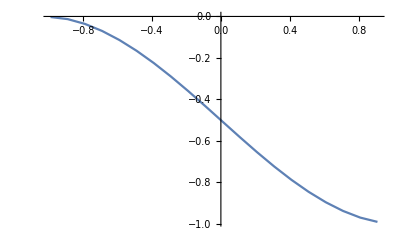

```mathematica
fig1=ListPlot[ans,Joined->True]
```

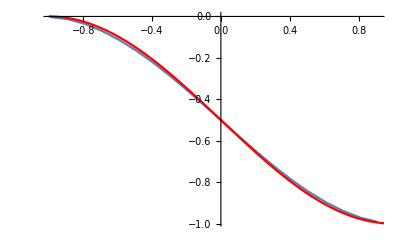

```mathematica
fig2=Plot[-0.5-0.5*Sin[x*2Pi/4],{x,-1,1},PlotStyle->{Red}];
Show[fig1,fig2]
```